## ГЛАВА1. Основы работы в системе Mathematica

### 1.1 Структура Mathematica

Mathematica состоит из двух основных частей - ядра (kernel), производящего  вычисления по заданным командам, и интерфейсного процессора (front end), задающего внешнее оформление и характер взаимодействия с пользователем и системой. Вся работа осуществляется в окне рабочего документа - блокнота (notebook), - внешний вид которого зависит от типа платформы и определяется интерфейсным процессором, своим для каждой платформы. Блокнот может содержать различные математические и специальные символы, графические объекты, однако внутреннее представление документа, с которым работает ядро программы, - всегда  неформатированный текст. Это позволяет легко переносить документы с одной платформы на другую.

### 1.2 Предварительная информация о встроенной справочной системе

LЫ i ш c і e х n э c ч e ш џ      C$M$0$0$0$1$-$2$2$0$7$2$0$0$2

#### Использование ядра

Справочные средства ядра вызываются командами ? и ??. Для получения информации о любом объекте, известном ядру системы, следует выполнить команду ?<имя объекта>. Например, выведем информацию о встроенной константе Pi :

```mathematica
?Pi
```

Pi is π, with numerical value ≃3.14159.

Для вывода более подробной информации используется ?? :

```mathematica
??Pi
```

Pi is π, with numerical value ≃3.14159.

Attributes[π]={Constant,Protected,ReadProtected}

Кроме того, при выполнении команды ? возможно использование шаблона - символа * в имени объекта:

```mathematica
?*Plot*
```

System`
ContourPlot | ListPlot | Plot | PlotJoined
DensityPlot | ListPlot3D | Plot3D | PlotLabel
ListContourPlot | ParametricPlot | Plot3Matrix | PlotPoints
ListDensityPlot | ParametricPlot3D | PlotDivision | PlotRange

Многие встроенные функции и команды в Mathematica имеют необязательные дополнительные параметры - опции. Вывести список всех опций той или иной функции, а также их значения по умолчанию позволяет команда Options[] :

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

### 1.3 Арифметические операции и их последовательность

Начнем работу в Mathematica с основных арифметических операций.

```mathematica
2+2
```

4

При первом вычислении загружается ядро Mathematica, которое производит все вычисления.
После того как ядро запущено попробуем сложить два 32-х разрядных числа

```mathematica
25011975435874958739485752161534+93582954263219754871911197685729
```

118594929699094713611396949847263

На этот раз результат появляется практически мгновенно.

expr1 + expr2 + ... + exprn  или Plus[expr1, expr2,..., exprn]
сложение выражений expr1, expr2, ..., exprn.

"Усложним" задачу и вставим в середину каждого из слагаемых знак вычитания:

```mathematica
2501197543587495-8739485752161534+9358295426321975-4871911197685729
```

-1751903979937793

expr1 - expr2  или  Subtract[expr1, expr2], а также
expr1 - expr2 - ... - exprn 
вычитание выражений.

- expr  или  Minus[expr]
изменить знак выражения expr.

Теперь разобьем все числа знаком умножения (пробел или *):

```mathematica
25011975 43587495-87394857 52161534+93582954 26321975-48719111 97685729
```

-5764314168230782

Обратите внимание, что в Mathematica умножение имеет привычный приоритет над сложением и вычитанием.

expr1  expr2  ...  exprn  или  Times[expr1, expr2,..., exprn]
вычисление произведения выражений expr1, expr2, ..., exprn.

Далее вставим в середину каждого числа знак деления:

```mathematica
2501/1975 4358/7495-8739/4857 5216/1534+9358/2954 2632/1975-4871/9111 9768/5729
```

-139784933181959569928678/67481856082797296274875

Здесь следует отметить, что в Mathematica деление имеет приоритет над умножением, хотя в данном случае это не оказывает влияния на итоговый результат.

expr1 / expr2  или  Divide[expr1, expr2]
деление выражений.

Наконец, лишим последнего шанса тех, кто решил вручную проверить правильность компьютерных вычислений, — в середину каждого числа добавим знак возведения в степень:

```mathematica
25^01/19^75 43^58/74^95-87^39/48^57 52^16/15^34+93^58/29^54 26^32/19^75-48^71/91^11 97^68/57^29
```

-(95625838569430126051863553949740902204554617817902954610132215940631391074770036302317933539971726857636689884307129166127322329467946802707360843083603329259541047723773471793699302239160376039560023234765109334106372213484550610823924135372487548037408338744459326112002307136010810527779649222827234064601774079513254038509632147597557599967688851845233202941076729679945988460599682826654385685065130846348076468463910484712538940000429687132394080272614847047912261756513430008718145746740075423734049557830549755819035309485670958955516732461317969994768404148513955346014260242855793944553923115313429029367118702394032891495113/958949203772924534127533842593529337200049829111198472305366735483593814431425298546817888010827413448995817247137720484385257483262823938061951729084389215764978786144763208276575420652609499879458172906760207734939235401259356736524707235522818202893073634398829806059270620784965711572918944824823034649143673971894392500674962667703616235882238285411686304978833230854813117382941669228395292928225370138745063342080000000000000000000000000000000000)

И в данном случае отметим, что возведение в степень имеет приоритет по отношению ко всем другим арифметическим операциям.

expr1 ^ expr2 ^ ... ^ exprn  или Power[expr1, expr2,..., exprn]
возведение выражений в степень.

Для изменения принятого порядка осуществления арифметических операций естественным образом используются круглые скобки.

### 1.4 Точные и приближенные вычисления

Все вычисления Mathematica по умолчанию производит точно:

```mathematica
(3/4)^(3333/70)
```

(26588814358957503287787 3^(43/70))/(39614081257132168796771975168 2^(8/35))

```mathematica
%^(70/3333)
```

3/4

Здесь знак % означает результат предыдущей операции. Вообще, выполняя небольшие по объему вычисления "на скорую руку", можно использовать символы %, %%, %%% для обращения к результатам команд, выполненных один, два или три шага назад, соответственно. Запись %n (или Out[n]) заменяет результат, находящийся в строке с меткой Out[n].
Для представления результата вычисления в виде числа с плавающей точкой используется команда N.

```mathematica
N[%%]
```

1.12495×10^-6

Эта команда по умолчанию выводит шесть значащих разрядов результата, из которых один — слева от десятичной точки, и необходимую степень 10. Командой N можно воспользоваться и для вывода большего количества знаков числа.

```mathematica
N[%%%,150]
```

1.12494502226821874375400743145175947389085801244825745598851545435499811377073446268230451249689874256658610901224676179978768269303558098974216243199×10^-6

N[expr]
вычисление приближенного значения выражения expr.

N[expr, n]
вычисление приближенного значения выражения c заданным количеством значащих цифр.

Еще один способ дать команду на приближенное вычисление — записать любой из операндов с десятичной точкой.

```mathematica
3.+2/3
```

3.66667

### 1.5 "Школьные" функции

Команда извлечения квадратного корня может быть записана в Mathematica тремя разными способами — с помощью функции Sqrt, возведением в степень 1/2 и с использованием стандартной палитры.

```mathematica
Sqrt[16]
16^(1/2)
√16
```

4

4

4

Следует обратить внимание, как Sqrt работает с квадратом символьной переменной в случаях, когда ее знак не определен и когда определен.

```mathematica
Sqrt[x^2]
```

√(x^2)

```mathematica
Sqrt[Abs[x]^2]
```

Abs[x]

Здесь Abs — функция модуля.

Sqrt[expr]
вычисление квадратного корня из выражения expr.

Abs[expr]
вычисление модуля выражения expr.

Mathematica различает заглавные и строчные буквы. Поэтому вызов встроенных команд (констант, директив и т. д.) необходимо осуществлять именно так, как это показано в примерах: название всегда с большой буквы, аргументы — в квадратных скобках.

Функция логарифма может вызываться с одним аргументом (натуральный логарифм) и с двумя (в этом случае первый аргумент — основание, по которому вычисляется логарифм второго аргумента).

```mathematica
Log[E^5]
```

5

```mathematica
Log[2,1024]
```

10

E — встроенная константа — основание натурального логарифма.

```mathematica
E-Exp[1]
```

0

Log[expr]
натуральный логарифм выражения expr.

Log[base, expr]
логарифм выражения expr по основанию base.

Exp[expr]
возведение числа e2,718281 в степень expr.

Кроме числа e в Mathematica определены и некоторые другие математические константы

Pi
число  π = 3,141592

### Задача 1.

Как узнать, что больше E^π или π^E?

LЫ i ш c і e х n э c ч e ш џ      C$M$0$0$0$1$-$2$2$0$7$2$0$0$2

Решение:

```mathematica
{E^π>π^E,π^E>E^π}
```

{True,False}

I
мнимая единица; комплексное число, квадрат которого равен -1

Infinity
константа, служащая для представления +∞.

Встроенная функция для вычисления факториала может вызываться двумя способами:

```mathematica
Factorial[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

Factorial[expr] или expr!
вычисление факториала выражения expr.

### Задача 2.

Вычислить π  с точностью до 50 знаков.

Решение:

```mathematica
N[π,50]//Timing
```

{0.,3.1415926535897932384626433832795028841971693993751}

### Задача 3.

Разложить на множители x^16-y^16.

Решение:

```mathematica
Factor[x^7-y^7]
```

(x-y) (x^6+x^5 y+x^4 y^2+x^3 y^3+x^2 y^4+x y^5+y^6)

### 1.6 Тригонометрические функции

Mathematica располагает набором встроенных тригонометрических функций, аргумент которых по умолчанию считается заданным в радианах.

```mathematica
Sin[13Pi/5]
```

√(5/8+(√5)/8)

Для перевода значения аргумента в градусную меру используется уже упомянутая константа Degree или символ ° из соответствующей палитры.

```mathematica
Cos[30Degree]
Cos[30°]
```

(√3)/2

(√3)/2

Sin[x], Cos[x], Tan[x], Cot[x], Sec[x], Csc[x]
тригонометрические функции Mathematica.

Шести тригонометрическим функциям в Mathematica соответствуют шесть обратных тригонометрических функций.

Они вычисляются как аналитические продолжения соответствующих тригонометрических функций действительного переменного. То есть, например, функция ArcSin для вещественного числа из отрезка  возвращает только значение главной ветви из промежутка 
[-π/2;π/2 ].

```mathematica
ArcSin[0.4]
```

0.411517

Функция ArcTan может быть записана с двумя аргументами x и y. В этом случае ее результатом будет значение -i Ln(x + iy)/(√(x^2)+y^2), которое при вещественных x и y равно аргументу комплексного числа x +iy :

```mathematica
ArcTan[√3/2,1/2]
ArcTan[-√3/2,-1/2]
```

π/6

-(5 π)/6

Знак ; на конце введенного выражения отменяет вывод результата вычисления на экран.
Ниже приведен код программы для изображения найденных углов.

```mathematica
$TextStyle={FontSize->14};
x=√3/2;y=1/2;
Show[Graphics[
{PointSize[0.03],
Point[{x,y}],Point[{-x,-y}],
{Thickness[.007],Dashing[{.025}],
Line[{{0,0},{x,y}}]},
{Thickness[.005],Dashing[{.012}],
Line[{{0,y},{x,y}}],
Line[{{0,-y},{-x,-y}}],
Line[{{x,0},{x,y}}],
Line[{{-x,0},{-x,-y}}]},
{Thickness[.007],Dashing[{.04}],
Line[{{0,0},{-x,-y}}]},
Circle[{0,0},0.35,{0,Pi/6}],
{Circle[{0,0},0.23,{-5Pi/6,0}]},{Text["-1/2",{.15,-1/2}],Text["-(√3)/2",{-(√3)/2,.15}]}         }],
Axes->True,AspectRatio->Automatic,PlotRange->{{-1.2,1.2},{-0.6,.6}},Ticks->{{{-√3/2,""},√3/2},{{-1/2,""},1/2}}];
Clear[x,y];
```

```mathematica
FontSize/.{FontSize->14}
```

14

### 1.7 Некоторые команды аналитических преобразований

Введем произвольное алгебраическое выражение:

```mathematica
((b+a)^3+(a+b)^2)^2
```

((a+b)^2+(a+b)^3)^2

Единственное, что сделала Mathematica в данном случае, — это переписала выражение согласно собственным правилам. Для более существенного преобразования выражения дадим системе команду:

```mathematica
Expand[%]
```

a^4+2 a^5+a^6+4 a^3 b+10 a^4 b+6 a^5 b+6 a^2 b^2+20 a^3 b^2+15 a^4 b^2+4 a b^3+20 a^2 b^3+20 a^3 b^3+b^4+10 a b^4+15 a^2 b^4+2 b^5+6 a b^5+b^6

Как и следовало ожидать, функция Expand совершила действие, соответствующее значению этого английского слова, — раскрытие скобок. 
Следующая команда  переписывает выражение в виде произведения:

```mathematica
Factor[%]
```

(a+b)^4 (1+a+b)^2

Теперь введем рациональное выражение:

```mathematica
expr1=(1+a)^2/((2+a)(1-a))
```

(1+a)^2/((1-a) (2+a))

```mathematica
Expand[expr1]
```

1/((1-a) (2+a))+(2 a)/((1-a) (2+a))+a^2/((1-a) (2+a))

```mathematica
ExpandAll[expr1]
```

1/(2-a-a^2)+(2 a)/(2-a-a^2)+a^2/(2-a-a^2)

На этот раз скобок не осталось ни в числителе, ни в знаменателе. Однако все выражение в результате оказалось записано в виде суммы дробей. Переписать его более компактно поможет функция приведения к общему знаменателю.

```mathematica
Together[%]
```

(-1-2 a-a^2)/(-2+a+a^2)

Мы также можем попросить Mathematica выяснить, какая форма записи того или иного выражения является (с точки зрения системы) наиболее простой.

```mathematica
expr2=(a^4 x+2 a^3 b x-2 a b^3 x-b^4 x)/(a^3+a^2 b-a b^2-b^3)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

Знак ; на конце введенного выражения отменяет вывод результата вычисления на экран.

```mathematica
Simplify[expr2]
```

(a+b) x

Функция Simplify производит раскрытие скобок, ряд других алгебраических преобразований выражения и в итоге возвращает его наиболее простой вид. Кроме того, еще одним аргументом этой функции можно задать условия на переменные, входящие в упрощаемое выражение. Такими условиями могут служить уравнения, неравенства, указание принадлежности переменной к той или иной области числовых значений.

```mathematica
Clear[x];Simplify[x/(√(x^2))]
Simplify[x/(√(x^2)),x<0]
```

x/(√(x^2))

-1

Однако, примененная к выражениям со специальными функциями или c функциями комплексного аргумента, команда Simplify не всегда оказывается достаточно эффективной.

```mathematica
expr3=-1/2 I (1/2 Log[-1/2-I/2]^2-1/2 Log[-1/2+I/2]^2+1/2 (-(I π)/2+Log[2])^2-1/2 ((I π)/2+Log[2])^2)-1/2 I (I π Log[2]+Log[-1/2-I/2] Log[2]-Log[-1/2+I/2] Log[2]-1/2 I π Log[2-2 I]+Log[-1/2+I/2] Log[2-2 I]-1/2 I π Log[2+2 I]-Log[-1/2-I/2] Log[2+2 I])
```

-1/2 ⅈ (1/2 Log[-1/2-ⅈ/2]^2-1/2 Log[-1/2+ⅈ/2]^2+1/2 (-(ⅈ π)/2+Log[2])^2-1/2 ((ⅈ π)/2+Log[2])^2)-1/2 ⅈ (ⅈ π Log[2]+Log[-1/2-ⅈ/2] Log[2]-Log[-1/2+ⅈ/2] Log[2]-1/2 ⅈ π Log[2-2 ⅈ]+Log[-1/2+ⅈ/2] Log[2-2 ⅈ]-1/2 ⅈ π Log[2+2 ⅈ]-Log[-1/2-ⅈ/2] Log[2+2 ⅈ])

```mathematica
Simplify[expr3]
```

-1/4 ⅈ (Log[-1/2-ⅈ/2]^2-Log[-1/2+ⅈ/2] (Log[-2+2 ⅈ]-2 Log[2-2 ⅈ])-ⅈ π (Log[2-2 ⅈ]+Log[2+2 ⅈ])+Log[-1/2-ⅈ/2] (-2 Log[2+2 ⅈ]+Log[4]))

### Задача 9.

Упростить выражение a^3+b^3+c^3-3abc при условии a+b+c=0.

Решение:

```mathematica
Clear[a,b,c]
```

```mathematica
Simplify[a^3+b^3+c^3-3a b c,a+b+c==0]
```

0

Применение функции Factor (функция раскладывает на множители) демонстрирует правильность работы Simplify.

```mathematica
Factor[a^3+b^3+c^3-3a b c]
```

(a+b+c) (a^2-a b+b^2-a c-b c+c^2)

Еще раз убедимся в этом, используя уже функцию GroebnerBasis.

```mathematica
GroebnerBasis[{a^3+b^3+c^3-3a b c,a+b+c},{a,b,c}]
```

{a+b+c}

Ещё задача для команды Simplify:

```mathematica
Simplify[Cos[π n],n∈Integers]
```

(-1)^n

Более мощным инструментом упрощения выражений является функция FullSimplify.

```mathematica
FullSimplify[expr3]
```

1/8 π Log[2]

Часто, когда в некотором выражении необходимо заменить какую-либо переменную (или несколько переменных) конкретным числовым значением или целой формулой, используется команда ReplaceAll или ее сокращенная запись /. :

```mathematica
ReplaceAll[(Sin[x]*x^3+x^2*y+3Log[x y])/(x+y)^Cos[x/y],{x->3,y->a+b}]
```

(3+a+b)^(-Cos[3/(a+b)]) (9 (a+b)+3 Log[3 (a+b)]+27 Sin[3])

Первый аргумент команды ReplaceAll — преобразуемое выражение, второй — правило подстановки (или список таких правил), которое записывается в виде переменная -> выражение и определяет какую замену проводить. Заметим, что ReplaceAll подставляет вместо указанных переменных заданные выражения и позволяет увидеть результат, но исходное выражение не изменяет.

```mathematica
expr=x^2+4x+5
```

5+4 x+x^2

```mathematica
expr/.x->Sin[x]
```

5+4 Sin[x]+Sin[x]^2

```mathematica
expr
```

5+4 x+x^2

### 1.8 Команды организации списков

Список — важнейший тип данных в Mathematica. Именно с помощью списков представляются векторы и матрицы, а также структуры данных более высоких размерностей. 
Простейший одномерный список представляет собой различные выражения Mathematica, записанные в фигурных скобках через запятую:

```mathematica
{a, 2b, x^2+Sin[y], 78.896}
```

{a,2 b,x^2+Sin[y],78.896}

Пара фигурных скобок представляет собой краткую запись команды List. Поэтому определение списка можно произвести и следующим образом:

```mathematica
List[a, 2b, x^2+Sin[y], 78.896]
```

{a,2 b,x^2+Sin[y],78.896}

В Mathematica имеется ряд команд, позволяющих создавать списки автоматически. 
Команду Range используют, как правило, для создания списка, содержимое которого — последовательность чисел. Если аргумент команды Range — произвольное число k (не обязательно целое), то результатом будет список из натуральных чисел, не превосходящих k:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Вызванная с двумя аргументами k1 и k2, команда Range создает список чисел от k1 до k2 с шагом 1:

```mathematica
Range[3.8,10.5]
```

{3.8,4.8,5.8,6.8,7.8,8.8,9.8}

При этом k1 и k2 могут быть символьными выражениями, но их разность — обязательно числовым:

```mathematica
Range[a,a+7]
```

{a,1+a,2+a,3+a,4+a,5+a,6+a,7+a}

Если команда вызвана с тремя аргументами, то третий определяет величину шага:

```mathematica
Range[-1,1,0.4]
```

{-1.,-0.6,-0.2,0.2,0.6,1.}

Допускается также одновременное задание нескольких списков:

```mathematica
Range[{1,3},{10,20},{2,3}]
```

{{1,3,5,7,9},{3,6,9,12,15,18}}

В этом случае созданные списки сами будут являться элементами списка.
Если элементы списка задаются по известному правилу (формуле), удобно использовать команду Table.

```mathematica
Table[(a+b)^i,{i,5}]
```

{a+b,(a+b)^2,(a+b)^3,(a+b)^4,(a+b)^5}

```mathematica
Table[2^i,{i,4,13}]
```

{16,32,64,128,256,512,1024,2048,4096,8192}

```mathematica
Table[Sin[i],{i,-Pi,Pi,.5}]
```

{-1.22465×10^-16,-0.479426,-0.841471,-0.997495,-0.909297,-0.598472,-0.14112,0.350783,0.756802,0.97753,0.958924,0.70554,0.279415}

Первым аргументом этой команды задается формула для создания элементов списка, включающая обычно некоторую переменную-счетчик (в данном случае i), которая для каждого элемента принимает определенное значение. Второй аргумент — итератор — определяет, в каких границах и с каким шагом счетчик должен изменяться. Итератор может включать от одного до четырех элементов, выполняющих те же функции, что и аргументы команды Range. Кроме того, может быть использовано несколько итераторов для формирования двумерных списков (матриц), а также списков более высоких размерностей:

```mathematica
lst=Table[i*j,{i,5},{j,5}]
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15},{4,8,12,16,20},{5,10,15,20,25}}

```mathematica
%//MatrixForm
```

(1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25)

Для отображения двумерного списка в традиционном матричном виде применяется команда MatrixForm. В приведенном примере эта команда записана в постфиксной форме. В такой форме в Mathematica могут вызываться любые команды, которые употребляются с одним аргументом.
Обращение к отдельным элементам списка производится с помощью команды Part (альтернативная запись — [[ ]]).

```mathematica
Part[lst,2]
lst[[2]]
lst[[2,3]]
```

Part::partd: Part specification lst⟦2⟧ is longer than depth of object.

lst⟦2⟧

Part::partd: Part specification lst⟦2⟧ is longer than depth of object.

lst⟦2⟧

Part::partd: Part specification lst⟦2,3⟧ is longer than depth of object.

lst⟦2,3⟧

### Задача 20.

Исследовать основные команды (операторы) работы с матрицами.

```mathematica
Clear[MM,x,i,j,t,a]
```

Создаем матрицу.

```mathematica
MM=Table[x[i]^j,{i,1,3},{j,0,2}]
```

{{1,x[1],x[1]^2},{1,x[2],x[2]^2},{1,x[3],x[3]^2}}

Выводим ее в обычном виде.

```mathematica
MM//MatrixForm
```

(1 | x[1] | x[1]^2
1 | x[2] | x[2]^2
1 | x[3] | x[3]^2)

Вычисляем определитель.

```mathematica
Det[MM]//Simplify
```

-(x[1]-x[2]) (x[1]-x[3]) (x[2]-x[3])

Вачисляем обратную матрицу.

```mathematica
Simplify[Inverse[MM]]//MatrixForm
```

((x[2] x[3])/((x[1]-x[2]) (x[1]-x[3])) | -(x[1] x[3])/((x[1]-x[2]) (x[2]-x[3])) | (x[1] x[2])/((x[1]-x[3]) (x[2]-x[3]))
-(x[2]+x[3])/((x[1]-x[2]) (x[1]-x[3])) | (x[1]+x[3])/((x[1]-x[2]) (x[2]-x[3])) | (x[1]+x[2])/((x[1]-x[3]) (-x[2]+x[3]))
1/((x[1]-x[2]) (x[1]-x[3])) | -1/((x[1]-x[2]) (x[2]-x[3])) | 1/((x[1]-x[3]) (x[2]-x[3])))

Другая матрица и другая форма ввода.

```mathematica
MM={{a,1,0},{-1,a,1},{0,-1,a}}
```

{{a,1,0},{-1,a,1},{0,-1,a}}

```mathematica
MM//MatrixForm
```

(a | 1 | 0
-1 | a | 1
0 | -1 | a)

Собственные значения.

```mathematica
Eigenvalues[MM]
```

Eigenvalues[MM]

Собственные векторы.

```mathematica
Eigenvectors[MM]
```

Eigenvectors[MM]

Характеристический полином.

```mathematica
CharacteristicPolynomial[MM,t]
```

CharacteristicPolynomial[MM,t]

Корни характеристического полинома.

```mathematica
Solve[2 a+a^3-2 t-3 a^2 t+3 a t^2-t^3==0,t]
```

{{t→a},{t→-ⅈ √2+a},{t→ⅈ √2+a}}

### Задача 21.

Из списка l={a,1,b,0,c,0,0,d} исключить все нулевые элементы.

Решение:

```mathematica
Clear[l,a,b,c,d]
```

```mathematica
l={a,1,b,0,c,0,0,d}
```

{a,1,b,0,c,0,0,d}

```mathematica
Delete[l,Position[l,0]]
```

{a,1,b,c,d}

### Задача 22.

Найти сумму отрицательных чисел в списке l={a,2,-1,b,c,-3}.

Решение:

```mathematica
Clear[l,a,b,c]
```

```mathematica
l={a,2,-1,b,c,-3}
```

{a,2,-1,b,c,-3}

```mathematica
Plus@@Select[l,Negative]
```

-4

### Задача 23.

Найти среднее квадратичное элементов списка l={-3,4,-7,0,11}.

Решение:

```mathematica
l={-3,4,-7,0,11}
```

{-3,4,-7,0,11}

```mathematica
√(∑_(i=1)^Length[l] l[[i]]^2)
```

√195

### Задача 24.

Преобразовать числовой список l в True, если в нем есть простые числа, или в False в противном случае.

Решение:

```mathematica
Clear[l]
```

```mathematica
l={6, 8 ,10,144,52}
```

{6,8,10,144,52}

```mathematica
Or@@PrimeQ/@l
```

False

```mathematica
l={6, 8 ,10,101,52}
```

{6,8,10,101,52}

```mathematica
Or@@PrimeQ/@l
```

True

### Задача 25.

Дана матрица M и столбец l. Как вставить l  k-м столбцом в матрицу?

Решение:

```mathematica
Clear[MM,l,k,a,b,c,d,f]
```

```mathematica
MatrInsert[M_,l_,k_]:=Transpose[Insert[Transpose[M],l,k]]
```

```mathematica
(M=Table[Random[Integer,{1,20}],{5},{5}])//MatrixForm
```

(9 | 4 | 17 | 8 | 13
4 | 3 | 6 | 19 | 18
13 | 14 | 20 | 2 | 9
10 | 11 | 14 | 8 | 17
9 | 10 | 6 | 14 | 15)

```mathematica
l={a,b ,c,d,f}
```

{a,b,c,d,f}

```mathematica
MatrInsert[M,l,2]//MatrixForm
```

(9 | a | 10 | 7 | 2 | 18
16 | b | 6 | 19 | 19 | 18
15 | c | 10 | 14 | 18 | 1
1 | d | 8 | 1 | 3 | 5
8 | f | 4 | 5 | 13 | 12)

```mathematica
MatrInsert[M,l,6]//MatrixForm
```

(9 | 10 | 7 | 2 | 18 | a
16 | 6 | 19 | 19 | 18 | b
15 | 10 | 14 | 18 | 1 | c
1 | 8 | 1 | 3 | 5 | d
8 | 4 | 5 | 13 | 12 | f)

### Задача 29.

Дан список переменных l={x,y,z} и список из значений m={1,2,3}. Получить список подстановок r={x→1,y→2,z→3}.

Решение:

```mathematica
Clear[l,m,x,y,z,a,b,c]
```

```mathematica
Subs[l_,m_]:=Thread[Rule[l,m]]
```

```mathematica
l={x,y,z}; m={1,2,3}
```

{1,2,3}

```mathematica
Subs[l,m]
```

{x→1,y→2,z→3}

```mathematica
Subs[l,{a,a+b,a+b+c}]
```

{x→a,y→a+b,z→a+b+c}

### 1.9 Некоторые функции математического анализа

Вычисление сумм, произведений, интегралов (определенных и неопределенных), производных (в том числе и частных), пределов функций и разложения в ряды Mathematica осуществляет как в числовой, так и в символьной форме.

Неопределенный интеграл:

```mathematica
Integrate[x/a^x,x]
```

-(a^-x (1+x Log[a]))/Log[a]^2

Определенный интеграл:

```mathematica
Integrate[x/Sin[x],{x,-1,1}]
```

1/2 ⅈ ((-2+π) π+4 ⅈ (ArcTanh[ⅇ^-ⅈ]+ArcTanh[ⅇ^ⅈ]+2 ⅈ PolyLog[2,ⅇ^ⅈ])+2 PolyLog[2,ⅇ^(2 ⅈ)])

В этом случае второй аргумент функции Integrate, содержащий информацию о переменной и пределах интегрирования, должен быть записан в виде списка.

Описанные функции интегрирования могут также быть вызваны нажатием соответствующей кнопки стандартной палитры:

```mathematica
∫_0^1 ((1-x)*Exp[x])/(1+x)ⅆx
```

(ⅇ-ⅇ^2-2 ExpIntegralEi[1]+2 ExpIntegralEi[2])/ⅇ

Для нахождения численного значения определенного интеграла используется функция NIntegrate:

```mathematica
NIntegrate[Cos[x]+Sin[Exp[x]],{x,0,Pi}]
```

0.644005

### Задача 5.

Найти интеграл ∫_a^b 1/(x-c)ⅆx, где a<c<b.

Интеграл существует только в смысле главного значения. Поэтому первоначально посмотрим существует ли соответствующая опция.

```mathematica
Options[Integrate]
```

{Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
Integrate[1/(x-c),{x,a,b},PrincipalValue->True,Assumptions->{0<a,a<c,c<b}]
```

Log[(-b+c)/(a-c)]

Функция вычисления частных производных — одна из немногих, для обозначения которых использовано не полное английское слово. Вот, например, как вычисляется обычная производная выражения

(1+cos x)/(sin x)

```mathematica
D[(1+Cos[x])/Sin[x],x]
```

-1-(1+Cos[x]) Cot[x] Csc[x]

А в следующем примере вычисляется частная производная

∂^2/(∂x∂y^2)ln(x+y)cos^y y

```mathematica
D[Log[x+y]*Cos[x]^y,x,{y,2}]
```

(2 Cos[x]^y)/(x+y)^3-(2 Cos[x]^y Log[Cos[x]])/(x+y)^2+(Cos[x]^y Log[Cos[x]]^2)/(x+y)+(y Cos[x]^(-1+y) Sin[x])/(x+y)^2+(2 (-Cos[x]^(-1+y)-y Cos[x]^(-1+y) Log[Cos[x]]) Sin[x])/(x+y)+Log[x+y] (-2 Cos[x]^(-1+y) Log[Cos[x]]-y Cos[x]^(-1+y) Log[Cos[x]]^2) Sin[x]

Все элементы дифференцируемого выражения, в которые переменные дифференцирования не входят, воспринимаются функцией D как константы.

Если Mathematica не в состоянии вычислить производную введенного выражения, то возвращается новое символьное выражение, обозначающее производную исходного.

```mathematica
D[a[x],x]
```

a'[x]

Здесь апостроф (') — краткая запись оператора Derivative[1] (общий вид — Derivative[n1, n2,...]), который служит для описания производных, взятых от выражений Mathematica.

### Задача 4.

Вычислить производную x^(x^x).

Решение:

```mathematica
D[x^(x^x),x]
D[x^x,x]
D[x,x]
```

x^(x^x) (x^(-1+x)+x^x Log[x] (1+Log[x]))

x^x (1+Log[x])

1

Функция Series, производящая разложение заданного выражения в степенной ряд в окрестности заданной точки, вызывается с двумя аргументами, которые структурно похожи на аргументы функции вычисления определенного интеграла: первый — исследуемое выражение, второй — список из трех элементов.

```mathematica
Series[Cos[Sin[a]+b],{a,0,5}]
```

Cos[b]-Sin[b] a-1/2 Cos[b] a^2+1/3 Sin[b] a^3+5/24 Cos[b] a^4-1/10 Sin[b] a^5+O[a]^6

В отличие от функции Integrate, в данном случае второй аргумент содержит информацию о том, по какой переменной производится разложение, в окрестности какой точки и до степени какого порядка.

Результат работы функции Series преобразуется к виду обычного многочлена командой Normal:

```mathematica
Normal[%]
```

Cos[b]-1/2 a^2 Cos[b]+5/24 a^4 Cos[b]-a Sin[b]+1/3 a^3 Sin[b]-1/10 a^5 Sin[b]

Команды суммирования и вычисления произведения могут вводиться как с клавиатуры, так и с помощью кнопок стандартной палитры

```mathematica
Sum[1/k^10,{k,Infinity}]
```

π^10/93555

```mathematica
∏_(i=2)^∞ (1-1/i^2)
```

1/2

### 1.10 Команды построения графиков

Для построения графика функции одной переменной используется команда Plot. Ее первый аргумент — выражение с одной символьной переменной. Второй аргумент (итератор) — одномерный список, несущий информацию о границах, в которых должна изменяться переменная при построении графика.

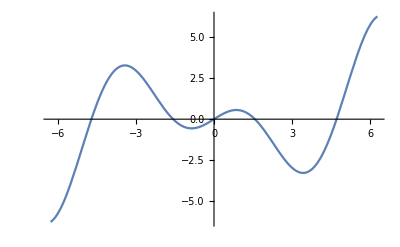

```mathematica
$TextStyle={FontSize->14};
p1=Plot[Cos[x]*x,{x,-2π,2π}]
```

Отметим, что результатом команды Plot является специальный графический объект Mathematica, для отображения которого на экране используется термин -Graphics-. Именно этот объект в данном случае будет значением переменной p1. Сам же рисунок, вообще говоря, является лишь "побочным эффектом" выполнения команды и его наличие или отсутствие на экране регулируется специальной опцией.

Команда Plot позволяет изобразить на одном рисунке графики сразу нескольких функций для одной и той же области изменения их общего аргумента:

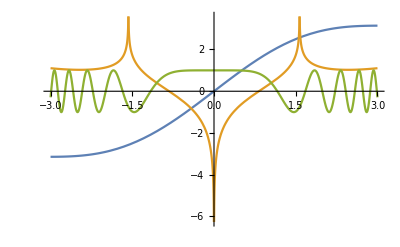

```mathematica
p2=Plot[{x+Sin[x],Log[Abs[x/(√Cos[x])]],Cos[x^3]},
                                                                                        {x,-3,3}]
```

Команда Plot3D для построения трехмерных графиков функций двух переменных имеет аналогичную форму записи, с той лишь разницей, что в ней необходимо указывать области изменения для двух переменных:

```mathematica
$TextStyle={FontSize->14};
p3=Plot3D[Sin[2x]*Sin[3x+y],
                                             {x,-1,1},{y,-3,3}]
```

-Graphics3D-

Для построения двумерных и трехмерных графиков функций, заданных параметрически, используются команды ParametricPlot и ParametricPlot3D соответственно.

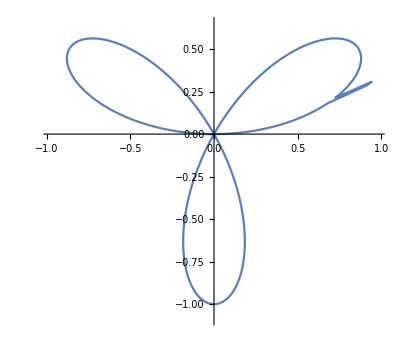

```mathematica
p4=ParametricPlot[{Cos[t] Sin[3 t], Sin[t] Sin[3 t]},{t,0,Pi}]
```

Команда ParametricPlot3D может использоваться для построения как кривых (один параметр), так и поверхностей (два параметра).

```mathematica
p5=ParametricPlot3D[{Sin[t/8]Cos[t],Sin[t/8]Sin[t],t/8},{t,0,8Pi},PlotPoints->1000]
```

-Graphics3D-

```mathematica
$TextStyle={FontSize->14};p6=ParametricPlot3D[{ Cos[p]+Sin[t] , Sin[p] + Cos[t],t},{p,0,2Pi},{t,-Pi,Pi}]
```

-Graphics3D-

Нечто среднее между двумерным и трехмерным графиком можно получить с помощью функции ContourPlot. Эта функция служит для построения контурного изображения трехмерной поверхности.

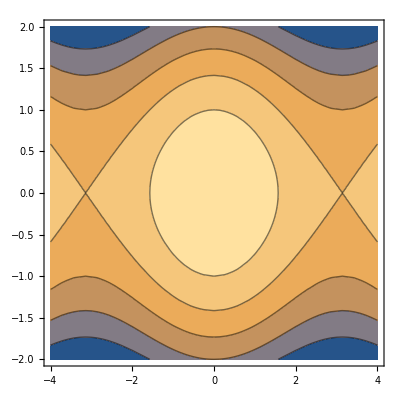

```mathematica
p7 = ContourPlot[Cos[x] - y^2, 
                    {x, -4, 4}, {y, -2, 2}]
```

Визуализация содержимого числовых списков производится командами ListPlot и ListPlot3D. Единственным аргументом команды ListPlot может быть числовой одномерный список. В построенном графике по горизонтальной оси будут откладываться порядковые номера элементов списка, а по вертикальной — значения этих элементов.

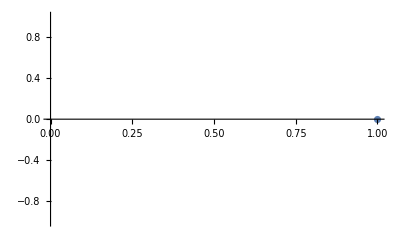

```mathematica
$TextStyle={FontSize->14};lst=Table[Sqrt[n]Sin[n]Cos[n],{n,0,1000}]Ж;
p8=ListPlot[lst]
```

Получив в качестве аргумента список числовых пар (двухэлементных списков), команда ListPlot изобразит точки с соответствующими парами координат.

{{-3,Cos[3]},{-5/2,Cos[5/2]},{-2,Cos[2]},{-3/2,Cos[3/2]},{-1,Cos[1]},{-1/2,Cos[1/2]},{0,1},{1/2,Cos[1/2]},{1,Cos[1]},{3/2,Cos[3/2]},{2,Cos[2]},{5/2,Cos[5/2]},{3,Cos[3]}}

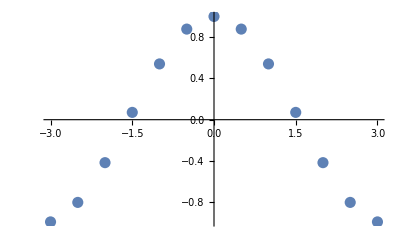

```mathematica
lst1=Table[{i,Cos[i]},{i,-3,3,1/2}]
p9=ListPlot[lst1,PlotStyle->PointSize[0.02]]
```

Опция PlotStyle в данном случае используется для установления размера выводимых точек в 2% от общей ширины рисунка.

Команды Plot, ParametricPlot, ParametricPlot3D позволяют выводить на одном рисунке графики нескольких функций одновременно. Для совмещения рисунков, полученных этими, а также и другими графическими командами, используется команда Show.

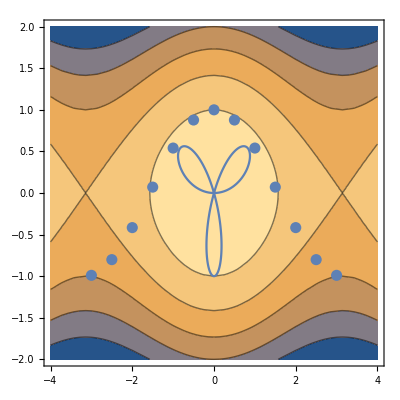

```mathematica
Show[p7,p4,p9]
```

Изображения перекрывают друг друга в том же порядке, в каком перечисляются соответствующие переменные.

### Задача 18.

Построить совместные графики функций f(x)=5 x^4-12 x^3+8 x^2+2  и её производной на интервале (-1,2). Сравните интервалы убывания и возрастания функции со знаком производной.

Решение:

```mathematica
D[5 x^4-12 x^3+8 x^2+2,x]
```

16 x-36 x^2+20 x^3

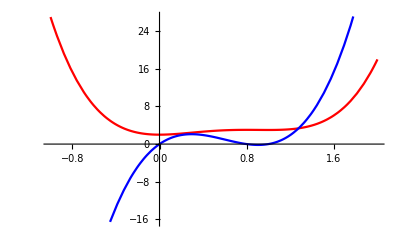

```mathematica
Plot[
{5 x^4-12 x^3+8 x^2+2,
16 x-36 x^2+20 x^3},
{x,-1,2},PlotStyle->{RGBColor[255,0,0],RGBColor[0,0,255]}]
```

### 1.11 Команды решения уравнений

Для компьютерной алгебраической системы наряду с возможностями преобразования символьных выражений не менее важным является умение решать уравнения. В Mathematica наиболее часто для этих целей используется команда Solve:

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

Первым аргументом записывается решаемое уравнение (или список уравнений в случае решения системы), второй аргумент — переменная (или список переменных), относительно которой требуется найти решение. Отметим, что при записи уравнения используется двойной знак равенства (инфиксная форма оператора Equal). Найденное решение представляется в виде двумерного списка правил подстановок, которым можно легко воспользоваться в дальнейших вычислениях.

```mathematica
x/.%
```

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.-Graphics-

В случае решения уравнения с одной символьной переменной второй аргумент может не указываться:

```mathematica
Solve[4 x^3+6 x^2+3x-4==0]
```

{{x→1/2 (-1+3^(2/3))},{x→-1/2-1/4 3^(2/3) (1-ⅈ √3)},{x→-1/2-1/4 3^(2/3) (1+ⅈ √3)}}

Команда Solve позволяет получить точное решение любого полиномиального уравнения до четвертой степени включительно и некоторых других.

```mathematica
Solve[2 x^20+ x^12==0]
```

{{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→0},{x→-(-1/2)^(1/8)},{x→(-1/2)^(1/8)},{x→-(-1)^(3/8)/2^(1/8)},{x→(-1)^(3/8)/2^(1/8)},{x→-(-1)^(5/8)/2^(1/8)},{x→(-1)^(5/8)/2^(1/8)},{x→-(-1)^(7/8)/2^(1/8)},{x→(-1)^(7/8)/2^(1/8)}}

Для полиномиального уравнения, точное алгебраическое решение которого получить нельзя, команда Solve возвратит решение следующего вида:

```mathematica
equ1=x^5+x^4+2x^3-x^2+4x+3==0;
sols=Solve[equ1,x]
```

{{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,1]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,3]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,4]},{x→Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,5]}}

Ограничимся лишь замечанием, что с каждым из полученных таким образом корней можно работать, как с точным числовым значением.

```mathematica
Expand[(Part[x/.sols,2]+b)^2]
```

b^2+2 b Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]+Root[3+4 #1-#1^2+2 #1^3+#1^4+#1^5&,2]^2

Получить приближенное значение этих корней с любой точностью также не составляет труда.

```mathematica
N[sols]
```

{{x→-0.58013},{x→-0.992048-1.51736 ⅈ},{x→-0.992048+1.51736 ⅈ},{x→0.782113-0.980699 ⅈ},{x→0.782113+0.980699 ⅈ}}

### Задача 6.

Найти решения системы уравнений x^2+y^2=1,x-y=1/2.

Решение:

```mathematica
Solve[{x^2+y^2==1,x-y==1/2},{x,y}]
```

{{x→1/4 (1-√7),y→1/4 (-1-√7)},{x→1/4 (1+√7),y→1/4 (-1+√7)}}

### Задача 11.

Решить уравнение x^3-2x+1=0.

Условие задачи — назначение функции Solve. Функция Solve будет пытаться решать уравнение в символьном виде. Напомним,что для системы Mathematica числа

2/3,√2

и тому подобные выражения, cоставленные из целых чисел, являются символами. Поэтому решения, получаемые функцией  Solve, подчас являются излишне громоздкими. Для того, чтобы просто численно решить уравнение с необходимым числом знаков после запятой, используется функция NSolve. Впрочем от решений, полученных функцией Solve, легко перейти к решениям, полученным функцией NSolve, но не наоборот.

```mathematica
Clear[x]
```

```mathematica
Solve[x^3-2x+1==0,x]
```

{{x→1},{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

```mathematica
NSolve[x^3-2x+1==0,x]
```

{{x→-1.61803},{x→0.618034},{x→1.}}

График многочлена

x^3-2x+1

можно использовать для того, чтобы найти решения графическим способом и сравнить с полученными.

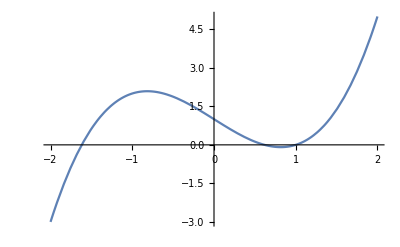

```mathematica
Plot[x^3-2x+1,{x,-2,2}]
```

### Задача 12.

Решить уравнение a x^2+b x+c=0 относительно параметров a, b, c.

Здесь ситуация несколько иная, чем в задаче 11. Необходимо проанализировать все варианты взаимного расположения параметров a,b и c. С этим успешно справляется функция Reduce (см.описание в Help).

```mathematica
Clear[x,a,b,c]
```

```mathematica
Reduce[a x^2+b x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

Булевы операции конъюнкции И (&&)и дизъюнкции ИЛИ (||), а также двуместные РАВНО (==) и НЕ РАВНО (≠) вполне понятны без дополнительных разъяснений и вывод результата работы функции Reduce легко интерпретируется.

### Задача 14.

Решить уравнение x^4+2 x^3-6 x^2+2x+1=0.

То же самое, что и в задаче 11. Можно только подметить, что многочлен обладает специальным свойством, поэтому существует изящный математический алгоритм решения предложенного уравнения. Этот алгоритм также может быть реализован средствами системы Mathematica.

Сначала найдем решение непосредственно, используя функцию Solve.

```mathematica
Clear[x,eqns,f,sol]
```

```mathematica
eqns=x^4+2 x^3-6 x^2+2x+1
```

1+2 x-6 x^2+2 x^3+x^4

```mathematica
Solve[eqns==0,x]
```

{{x→1},{x→1},{x→-2-√3},{x→-2+√3}}

Теперь заметим, что функция f(x) удовлетворяет следующему условию :

f(1/x)x^4=f(x).

Действительно,

```mathematica
f[x_]=x^4+2 x^3-6 x^2+2x+1
```

1+2 x-6 x^2+2 x^3+x^4

```mathematica
FullSimplify[f[1/x] x^4==f[x]]
```

True

Воспользуемся этим, чтобы найти решения другим способом.

```mathematica
sol=Flatten[Solve[Simplify[Expand[eqns/x^2],x+1/x==y]==0,y]]
```

{y→-4,y→2}

```mathematica
Solve[x+1/x==sol[[2]][[2]],x]
```

{{x→1},{x→1}}

```mathematica
Solve[x+1/x==sol[[1]][[2]],x]
```

{{x→-2-√3},{x→-2+√3}}

Смысл второго способа решения возвратных уравнений в том, что он позволяет находить в квадратурах решения возвратных уравнений, если их степень не превышает 8. Функция Solve решить возвратное уравнеие степени выше 4 в квадратурах не сможет, поскольку она не различает внутреннюю структуру многочлена. Этот пример, в частности, подтверждает тот очевидный факт, что никакая система компьютерной алгебры не в состоянии заменить профессионально подготовленного специалиста. А вот для специалиста она может стать незаменимым помощником.

### Задача 15.

Выяснить, является ли многочлен  x^4+4 x^3-2 x^2-12x+9 точным квадратом, т.е. можно ли подобрать три числа p, q, r так, чтобы имело место тождество x^4+4 x^3-2 x^2-12x+9=(p x^2+q x+r)^2.

Решение:

```mathematica
Clear[x,p,q,r,a,b,c,d,f]
```

```mathematica
Factor[x^4+4 x^3-2 x^2-12x+9]
```

(-1+x)^2 (3+x)^2

Данный многочлен является полным квадратом cо следующими коэффициентами p, q, r:

```mathematica
SolveAlways[x^4+4 x^3-2 x^2-12x+9==(p x^2+q x+r)^2,x]
```

{{p→-1,r→3,q→-2},{p→1,r→-3,q→2}}

А теперь в общем случае:

```mathematica
SolveAlways[a x^4+b x^3+c x^2+d x+f==(p x^2+q x+r)^2,x]
```

{{a→p^2,b→2 p q,c→q^2+2 p r,d→2 q r,f→r^2}}

Функция SolveAlways находит соотношения между одной группой переменных (в данном случае p,q,r,a,b,c,d,f) при условии, что равенство выполняется для всех значений другой группы переменных (в данном случае x).

### Задача 16.

Показать, что многочлен x^2+y^2+z^2 нельзя представить в виде произведения (ax+by+cz)(Ax+By+Cz) ни при каких вещественных или комплексных числах a,b,c,A,B,C.

Решение:

```mathematica
SolveAlways [x^2+y^2+z^2==(a x+b y+c z)(A x+B y+C z),{x,y,z}]
```

{}

Проверим, что действительно получается пустое множество решений

```mathematica
Collect[Expand[x^2+y^2+z^2-(a x+b y+c z)(A x+B y+C z)],x]
```

(1-a A) x^2+y^2-b B y^2-B c y z-b C y z+z^2-c C z^2+x (-A b y-a B y-A c z-a C z)

```mathematica
lst=CoefficientList[Expand[x^2+y^2+z^2-(a x+b y+c z)(A x+B y+C z)],x]
```

{y^2-b B y^2-B c y z-b C y z+z^2-c C z^2,-A b y-a B y-A c z-a C z,1-a A}

Получаем систему уравнений

```mathematica
ur=(#==0)&/@lst
```

{y^2-b B y^2-B c y z-b C y z+z^2-c C z^2==0,-A b y-a B y-A c z-a C z==0,1-a A==0}

```mathematica
Solve[ur,{a,b,c}]
```

{}

Данная система уравнений не имеет решений, а значит не существует требуемого представления.

Однако для нахождения численного решения уравнения существуют и специализированные средства.

Команда NSolve находит численно все решения полиномиального уравнения или системы таких уравнений.

```mathematica
NSolve[equ1,x]
```

{{x→-0.992048-1.51736 ⅈ},{x→-0.992048+1.51736 ⅈ},{x→-0.58013},{x→0.782113-0.980699 ⅈ},{x→0.782113+0.980699 ⅈ}}

Третьим аргументом этой команды может указываться число, соответствующее количеству числовых знаков в получаемом результате.

Если в решении уравнения не помогают ни Solve, ни NSolve можно воспользоваться функцией численного отыскания корня FindRoot. Используя метод Ньютона, эта функция находит один из корней уравнения по заданному начальному приближению.

```mathematica
FindRoot[Cos[Log[x]]-Sin[x/2],{x,1}]
FindRoot[Cos[Log[x]]-Sin[x/2],{x,0.5}]
```

{x→1.87954}

{x→0.233639}

В NSolve и FindRoot первым аргументом может быть не только уравнение (в отличие от Solve), но и функция, корни которой необходимо найти.

Для решения полиномиальных уравнений может быть использована и функция Roots, которая действует аналогично Solve, но позволяет получить результат в иной форме.

```mathematica
Roots[x^3+3x^2-x-6==0,x]
```

x==1/2 (-1-√13)||x==1/2 (-1+√13)||x==-2

Решение записывается в виде выражения, результатом которого после подстановки конкретного значения x будет одна из встроенных логических констант — True (истина) или False (ложь). В данном случае связка логических операций записана с использованием уже знакомой нам команды Equal (которая может использоваться не только для записи уравнений, но и как самостоятельная логическая команда для сравнения двух числовых величин) и команды Or (инфиксная форма ||). Отметим, что Or (логическое или) имеет более низкий приоритет по сравнению с Equal. Результат True, как легко догадаться, получится только в случае, когда в качестве значения x будет подставлен один из корней уравнения.

```mathematica
%/.x->-2
```

True

Команда Roots в сочетании с командой ToRules позволяет получить решения уравнения в виде более привычного двумерного списка правил подстановок.

```mathematica
{ToRules[%%]}
```

{{x→1/2 (-1-√13)},{x→1/2 (-1+√13)},{x→-2}}

### 1.12 Выражения и переменные

Ранее мы уже пользовались различными переменными, обозначая ими результаты выполненных команд, которые могли потребоваться в дальнейшей работе. При этом набор символов, используемый как переменная, мог обозначать и символьное выражение, и целое уравнение, и даже график функции: пользователю не надо заботиться об объявлении переменной того или иного типа и следить за резервированием для нее памяти.

Отдельные числа или символы, уравнения и графики и т. п. — все эти объекты являются выражениями Mathematica, для которых предусмотрены единые правила записи. Одни выражения строятся посредством комбинирования других, более мелких. Наиболее мелкие (атомарные) выражения в Mathematica — это числа (целые, вещественные, рациональные или комплексные), символы и строки.

Рассмотрим, например, четыре числа: целое, вещественное (т.е. в терминологии Mathematica — с десятичной точкой), рациональное и комплексное.

```mathematica
FullForm[34]
FullForm[66.8]
FullForm[2/3]
FullForm[1+I]
```

34

66.8

Rational[2,3]

Complex[1,1]

Команда FullForm отображает стандартную форму представления выражений в Mathematica (далеко не все команды используются в стандартной форме, и, например, знак "+" — инфиксная форма команды Plus — не относится к стандартной записи операции сложения). Полученные результаты говорят о том, что рациональные и комплексные числа имеют в Mathematica несколько иное представление, нежели целые и вещественные. И хотя числа всех этих четырех типов считаются атомарными выражениями, для описания рациональных и комплексных явным образом используются заголовки: эти типы описываются "командами" Rational и Complex соответственно. Альтернативные варианты ввода таких чисел — с помощью наклонной черты "/" и константы I — реализованы для удобства. Поскольку в Mathematica любая команда с двумя аргументами f[expr1, expr2] может быть записана в инфиксной форме

expr1~f~expr2,

то, вообще говоря, для определения рациональной дроби возможна также следующая не очень удобная конструкция:

```mathematica
2~Rational~3
```

2/3

Атомарное выражение "символ" — это любая последовательность букв (напомним, что Mathematica различает строчные и прописные буквы), цифр и знака $. Символ не может начинаться с цифры — такая запись интерпретируется как умножение этой цифры на символ из остальных знаков. Во многих приведенных выше примерах различные символы использовались в качестве идентификаторов переменных.

Еще один тип атомарного выражения — "строка" — это последовательность ASCII-символов, заключенная в кавычки.

Команда FullForm, примененная к произвольным символам и строкам, как и следовало ожидать, не дает никакого раскрытия их внутренней структуры.

```mathematica
FullForm[x1]
FullForm[f2RT$s]
FullForm["This is a string"]
FullForm["строка"]
```

x1

f2RT$s

"This is a string"

"\:0441\:0442\:0440\:043e\:043a\:0430"

В Mathematica всякое выражение либо является атомарным, либо имеет следующую структуру f[a_1,a_2,...,a_n],где

a_1,a_2,...,a_n  — выражения Mathematica,n — длина выражения. Заголовок f может быть выделен из выражения командой Head.

```mathematica
expr=(a+b*c)^2-Sin[d-e/f]
FullForm[expr]
Head[expr]
```

```mathematica
(a+b c)^2-Sin[d-e/f]
```

Plus[Power[Plus[a,Times[b,c]],2],Times[-1,Sin[Plus[d,Times[-1,e,Power[f,-1]]]]]]

Plus

Доступ к элементам  осуществляется с помощью команды Part.

```mathematica
Part[expr,1]
expr[[2]]
```

(a+b c)^2

-Sin[d-e/f]

Количество структурных элементов  (длина выражения) может быть определено командой Length.

```mathematica
Length[expr]
```

2

Каждый из элементов выражения сам является выражением, имеет заголовок и может быть разделен на структурные части. Такое выделение структурных частей можно продолжать до получения только атомарных выражений.

```mathematica
expr[[2,2,1,2,3,1]]
```

f

Атомарные выражения имеют только заголовки — Integer, Real, Symbol, String. Рациональные и комплексные числа представляют собой особые атомарные выражения: в своем представлении они имеют и заголовок, и структурные части, но команды Part[expr, 1] или Part[expr, 2] к выражениям с заголовками Rational и Complex не применяются.

Заголовок любого выражения expr считается его нулевым структурным элементом, поэтому аналогом команды Head[expr] служит команда Part[expr, 0] (или expr[[0]]).

Существует способ искусственно добавить к ряду выражений один и тот же заголовок. Для этого используется команда Map (краткая инфиксная форма — /@), первый аргумент которой — выражение, выполняющее роль заголовка, второй — преобразуемое выражение или список выражений.

```mathematica
Map[ddd,{a,b,c,d}]
```

{ddd[a],ddd[b],ddd[c],ddd[d]}

В случае, когда первый аргумент является наименованием какой-либо функции, такая операция автоматически приводит к применению этой функции ко второму аргументу или (в случае списка) к каждому его элементу.

```mathematica
Length/@
{Sin[x^2-y],a+b,Solve[x^2+x-4==0,x]}
```

{1,2,2}

Итак, переменной (как правило, атомарным символом) может быть обозначено всякое выражение. Производится эта операция с помощью команды немедленного присвоения Set[expr1, expr2] (=). В этом случае вычисление второго элемента выражения (правой части в записи присвоения) производится немедленно и результат присваивается первому элементу. Если же необходимо присвоить переменной не результат, а исходное значение выражения, то используется команда отложенного присвоения Set-

Delayed[expr1, expr2] (:=).

В следующем примере значение переменной a — псевдослучайное вещественное число из интервала [0,1] , а значение переменной b — команда, вычисляющая псевдослучайное число заново всякий раз, когда в вычислениях используется символ b.

```mathematica
a=Random[]
```

0.467838

```mathematica
b:=Random[]
```

```mathematica
a-a
b-b
```

0.

-0.266092

Для освобождения переменной от значения служит команда Clear.

```mathematica
Clear[a,b]
a
b
```

a

b

В Mathematica существует также несколько специальных команд для изменения значений числовых переменных.

```mathematica
{a=1,a++,a}
```

{1,1,2}

```mathematica
{b=1,++b,b}
```

{1,2,2}

```mathematica
{c=3,c*=4,c}
```

{3,12,12}

### Задача 7.

Упростить логическое выражение
(¬x∧¬y∧¬z)∨(x∧y∧z)∨(x∧¬y∧z)∨(¬x∧¬y∧z)∨(¬x∧y∧z)∨(¬x∧y∧¬z).

Функция LogicalExpand непосредственно решает,рассматриваемую задачу.Это ее назначение применения (см.Help).

```mathematica
LogicalExpand[!x&&!y&&!z||x&&y&&z||x&&!y&&z||!x&&!y&&z||!x&&y&&z||!x&&y&&!z]
```

z||!x

Команды

Increment[var] (var++),
PreIncrement[var] (++var),
Decrement[var] (var--),
PreDecrement[var] (--var),
AddTo[var, number] (var += number),
TimesBy[var, number] (var = number)

и некоторые другие служат для оперативного изменения значений числовых переменных в процессе выполнения более сложных вычислений.